```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
```

/Users/pjoot/project/figures/phy456-qmII

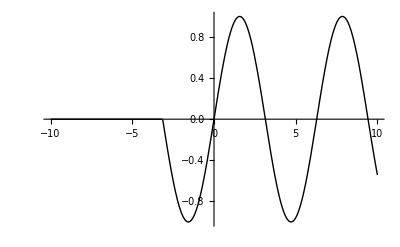

```mathematica
unitStepSine = Plot[  UnitStep[x+ Pi]  Sin[  x ], {x, -10, 10}, PlotStyle->{Thick,Black}, Ticks -> None]
```

```mathematica
peeters`exportForLatex["unitStepSine",unitStepSine]
```

{unitStepSine.eps,unitStepSinepn.png}